The Nine-Qubit Quantum Error-Correction Code |

Bit-Flip Errorspaclet:Q3/tutorial/NineQubitCode#818099018 | Arbitrary Errorspaclet:Q3/tutorial/NineQubitCode#18451360
Phase-Flip Errorspaclet:Q3/tutorial/NineQubitCode#2033391278 |

See also Section 6.1 of the Quantum Workbook (Springer, 2022)https://doi.org/10.1007/978-3-030-91214-7.

The nine-qubit code by Peter Shor (1995) is an elementary example of quantum error-correction codes. It require a relatively large use of resources for the given error types, and in this sense, there are more efficient methods. However, its simple structure makes it easy to grasp the fundamental ideas behind the quantum error-correction codes, including how to encode quantum information to protect against errors, how to detect error syndrome, and how to recover quantum information from corrupted data.

QuantumCircuit | Represents a quantum circuit.
CNOT | The controlled-NOT gate.
Hadamard | The Hadamard gate.

Q3 functions related to the subject.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Bit-Flip Errors

Suppose that the quantum computer is subjected to quantum noise that flips the the basis states of the individual qubits, |0⟩ ↔ |1⟩, with probability p. The error is called the bit-flip error, and we are to examine the code to correct it.

To protect a single-qubit state ψ=0 c_0+1 c_1 against the bit-flip error, one has to encode it to multiple qubits. For example, one encodes ψ to the three-qubit state ψ̄=000 c_0+111 c_1. In this encoding, the logical basis states are

OverBar[0]:=000 ,    OverBar[1]:=111 ,

and these are distinguished from the physical basis states 0 and 1 of each qubit. Therefore, the subspace spanned by the two logical basis states is the code space. The projection onto the code space is given by

P_0:=000000+111111 .

The encoding procedure can be achieved through a quantum circuit

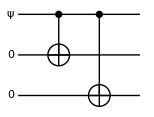

or

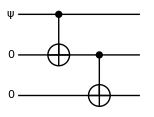
-Graphics-.

To see how this encoding protects against the bit-flip error, suppose that the error occurs on the first qubit, whereby the error is described by the operator, X⊗I⊗I. Then, the encoded state changes to (ψ̄)_1=100 c_0+011 c_1. This state is orthogonal to the original state ψ̄, and in principle can be discriminated through a proper measurement. Indeed, the measurement associated with the projection

P_1:=100100+011011

can do it. Similarly, bit flips on the second and third qubit modify the encoded state into (ψ̄)_3=010 c_0+101 c_1 and (ψ̄)_3=001 c_0+110 c_1, respectively. These states reside in the subspaces corresponding to the projection operators

P_2:=010010+101101

and

P_3:=001001+110110,

respectively. As the bit-flip errors on individual qubits bring the encoded state ψ̄ to mutually orthogonal subspaces, or equivalently, P_i P_j=δ_(i j)P_j, one can set up a projection measurement that is described by projectors P_0,P_1,P_2,P_3 to determine the qubit on which the error has actually occurred (if at all). The measurement result is referred to as the error syndrome, and its measurement is referred to as the error-detection procedure.

It is interesting to note that the states ψ̄, (ψ̄)_1, (ψ̄)_2, and (ψ̄)_3 are all simultaneous eigenstates of the two observables

M_1:=Z⊗Z⊗I ,     M_2:=I⊗Z⊗Z .

Furthermore, since they are mutually orthogonal, they must belong to different pairs of eigenvalues of M_1 and M_2. Indeed, we see by inspection that they belong to pairs of eigenvalues (1, 1), (−1, 1), (−1, −1) and (1, −1), respectively. Therefore, the measurements of M_1 and M_2 produce exactly the same information regarding the error syndrome as the projection measurement associated with P_j outlined above. Although less obvious at this stage, this method of error-detection is easier to extend—and more closely related to the stabilizer formalism—than the above measurement in terms of the projectors P_j, so we will focus mainly on this method from now on.

It is crucial for the error-detection procedure to not reveal the details of the encoding, i.e., the amplitudes c_0 and c_1 in ψ̄. Otherwise, measuring the error syndrome would destroy the superposition in the quantum states. For example, the measurement of M_1 just compares the values for the first and second qubit, giving +1 if the values are the same and −1 if they are different, without revealing the individual values. Similarly, measuring M_2 only compares the values of the second and third qubit, but it does not disclose the individual values. Nevertheless, it is still possible to determine where the error occurs. For example, suppose that the quantum noise flips the first qubit. Comparing the values of the first two qubits determines that the error has occurred on either of the first qubits, but not on exact which. Comparing the second and third qubit indicates that the error has occurred on neither (or both) of the qubits. Assuming that the error rate is sufficiently low, the two comparisons can successfully predict that the error occurred on the first qubit.

Once the error-detection procedure identifies the error syndrome, the next step is to correct the error and recover the original encoded state ψ̄. This step is called the recovery procedure. For the bit-flip error, the recovery procedure is quite simple. Depending on the qubit that has an error, one just has to apply the gate operation X ⊗I ⊗I, I ⊗X ⊗I, or I ⊗I ⊗X; or, of course, just do nothing if the measurement indicates that no error has occurred.

Following the error-correction procedure shown above, the original state is successfully recovered as long as either no error occurs at all or the bit-flip error occurs on only one of the three qubits. The probability for successful recovery is thus given by (1 − p)^3 + 3p(1 − p)^2 = 1 − 3p + 2 p^2. Compared to a probability of 1−p for a bare state, i.e., a non-encoded state, to remain uncorrupted, the encoding and subsequent error-correction procedure improves the reliability of the storage of the quantum state as long as p<1/2. This rather crude estimation of the quality of the quantum error-correction procedure provides a first impression how the quantum error-correction code works, and a more complete analysis will follow later.

### Demonstration

Suppose that we want to encode a single-qubit state to protect it against the bit-flip error.

```mathematica
vec=ProductState[S[1]->{c[0],c[1]},"Label"->Ket[ψ]]
```

(c_0 0+c_1 1)_S_1

The encoding is achieved by a quantum circuit model of the form.

```mathematica
qc=QuantumCircuit[vec,LogicalForm[Ket[],S@{2,3}],CNOT[S[1],S[2]],CNOT[S[1],S[3]]]
```

-Graphics-

```mathematica
out=DefaultForm@ExpressionFor[qc];
out//LogicalForm
```

c_0 0_S_10_S_20_S_3+c_1 1_S_11_S_21_S_3

Here is another quantum circuit model giving the same encoding.

```mathematica
qc2=QuantumCircuit[vec,LogicalForm[Ket[],S@{2,3}],CNOT[S[1],S[2]],CNOT[S[2],S[3]]]
```

-Graphics-

```mathematica
out2=DefaultForm@ExpressionFor[qc2];
out2//LogicalForm
```

c_0 0_S_10_S_20_S_3+c_1 1_S_11_S_21_S_3

Consider a bit-flip error occurs randomly

```mathematica
errors=Join[{1},S[{1,2,3},1]]
opE=RandomChoice[errors]
new=opE**out;
new//LogicalForm
```

{1,S_1^x,S_2^x,S_3^x}

S_3^x

c_0 0_S_10_S_21_S_3+c_1 1_S_11_S_20_S_3

This gives the error syndrome.

```mathematica
out1=Measurement[op1=S[1,3]**S[2,3]]@new;
out2=Measurement[op2=S[2,3]**S[3,3]]@new;
LogicalForm[out1,S@{1,2,3}]/.{c[0]Conjugate[c[0]]+c[1]Conjugate[c[1]]->1}
LogicalForm[out2,S@{1,2,3}]/.{c[0]Conjugate[c[0]]+c[1]Conjugate[c[1]]->1}
Readout@{op1,op2}
```

c_0 0_S_10_S_21_S_3+c_1 1_S_11_S_20_S_3

c_0 0_S_10_S_21_S_3+c_1 1_S_11_S_20_S_3

{0,1}

Phase-Flip Errors

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

As was already mentioned, a quantum state is a superposition of the logical basis state, and any modulation of the superposition coefficients without altering the logical basis states results in an error. In particular, a mere change in the relative phase in the coefficients leads to a deviation from the original state even though it does not change the occupation probabilities in the logical basis states. Let us consider an extreme case where the relative phase of a single qubit is shifted by π—the relative sign of the superposition coefficients is flipped from +1 to −1, and vice versa—with probability p. It is called the phase-flip error, and the corresponding error operator is Z. Such an error is particularly interesting because it has no classical counterpart since classically, the phase does not play any role.

Nevertheless, the phase-flip error is essentially no different from the bit-flip error. This becomes immediately clear when one observes that the phase-flip error switches the states ±:=(0±1)/√2 to each other. Therefore, a change of basis from {0,1} to {+,-} just converts the phase-flip error to the bit-flip error, which has already been addressed above. Apart from the proper choice of basis, the full error-correction procedure (including encoding, error-detection, and recovery) is the same as protecting against bit-flip errors. It seems ironic that the phase-flip error, which appears to be genuinely a quantum problem, can be countered by a basis change, another feature of quantum mechanics with no classical equivalent. This fact suggests that all types of errors can be handled on an equal footing, and it further inspires ideas for how to protect against general quantum noise.

Although it is already clear from the above observations, for the sake of later use, we construct the procedure to protect against phase-flip errors. The encoding chooses

OverBar[0]:=+++ ,    OverBar[1]:=---

as the local basis states. The unitary transformation to implement the encoding
can be described as a quantum circuit of the form

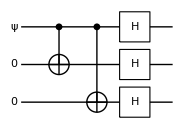

or

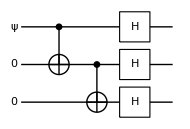
-Graphics-.

Compared to the corresponding quantum circuits for the bit-flip correction code, the above quantum circuits have additional Hadamard gates, H^(⊗3), to account for the basis change mentioned above. Phase-flip errors on one or fewer qubits of the three can be detected by measuring the observables

M'_1=H^(⊗3)M_1 H^(⊗3)=X⊗X⊗I ,

M'_2=H^(⊗3)M_2 H^(⊗3)=I⊗X⊗X ,

as H Z H=X. That is, the phase-flip error on the first, second, and third qubit leads to the measurement results (−1, 1), (−1, −1), and (1, −1), respectively, with an outcome that will be (1,1) if no error occurs. Once the error syndrome is diagnosed, the error can be fixed by applying the recovery operator I⊗I⊗I (doing nothing), Z⊗I⊗I, I⊗Z⊗I, or I⊗I⊗Z as H X H=Z.

### Demonstration

Suppose that we want to encode a single-qubit state to protect it against the phase-flip error.

```mathematica
vec=ProductState[S[1]->{c[0],c[1]},"Label"->Ket[ψ]]
```

(c_0 0+c_1 1)_S_1

The encoding is achieved by a quantum circuit model of the form.

```mathematica
qc=QuantumCircuit[vec,LogicalForm[Ket[],S@{2,3}],CNOT[S[1],S[2]],CNOT[S[1],S[3]],S[{1,2,3},6]]
```

-Graphics-

```mathematica
out=DefaultForm@ExpressionFor[qc];
out//LogicalForm
```

((c_0+c_1) 0_S_10_S_20_S_3)/(2 √2)+((c_0-c_1) 0_S_10_S_21_S_3)/(2 √2)+((c_0-c_1) 0_S_11_S_20_S_3)/(2 √2)+((c_0+c_1) 0_S_11_S_21_S_3)/(2 √2)+((c_0-c_1) 1_S_10_S_20_S_3)/(2 √2)+((c_0+c_1) 1_S_10_S_21_S_3)/(2 √2)+((c_0+c_1) 1_S_11_S_20_S_3)/(2 √2)+((c_0-c_1) 1_S_11_S_21_S_3)/(2 √2)

To compare the above result with the desired state, let us construct the encoding explicitly.

```mathematica
new=ProductState[S@{1,2,3}->{1,1}/Sqrt[2]]c[0]+ProductState[S@{1,2,3}->{1,-1}/Sqrt[2]]c[1]
```

c_1 (0/(√2)-1/(√2))_S_1⊗(0/(√2)-1/(√2))_S_2⊗(0/(√2)-1/(√2))_S_3+c_0 (0/(√2)+1/(√2))_S_1⊗(0/(√2)+1/(√2))_S_2⊗(0/(√2)+1/(√2))_S_3

```mathematica
out-new//Elaborate
```

0

Here is another quantum circuit model giving the same encoding.

```mathematica
qc2=QuantumCircuit[vec,LogicalForm[Ket[],S@{2,3}],CNOT[S[1],S[2]],CNOT[S[2],S[3]],S[{1,2,3},6]]
```

-Graphics-

```mathematica
out2=DefaultForm@ExpressionFor[qc2];
out2//LogicalForm
```

((c_0+c_1) 0_S_10_S_20_S_3)/(2 √2)+((c_0-c_1) 0_S_10_S_21_S_3)/(2 √2)+((c_0-c_1) 0_S_11_S_20_S_3)/(2 √2)+((c_0+c_1) 0_S_11_S_21_S_3)/(2 √2)+((c_0-c_1) 1_S_10_S_20_S_3)/(2 √2)+((c_0+c_1) 1_S_10_S_21_S_3)/(2 √2)+((c_0+c_1) 1_S_11_S_20_S_3)/(2 √2)+((c_0-c_1) 1_S_11_S_21_S_3)/(2 √2)

Arbitrary Errors

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

So far, we have considered specific types of errors, the bit-flip and phase-flip errors. Obviously, realistic errors are far more general, not only in terms of the above two but also with any continuous change of the complex amplitudes in superposition of quantum states. It may sound rather surprising at first glance, but it turns out that roughly speaking, if a quantum error-correction code can correct the bit-flip and phase-flip errors, then it can correct any arbitrary errors. Before we introduce the precise statement and the corresponding construction of the quantum error-correction code in subsequently sections, we provide an example here: Shor’s 9-qubit code. This code just builds upon the bit-flip and phase-flip correction codes discussed above, and yet it corrects completely arbitrary single-qubit errors.

According to the discussion above, protecting against the bit-flip and phase- flip error each requires for three qubits to encode one bit of physical quantum state. Hence, the encoding in Shor’s code needs 9 qubits to protect against both types of errors and their possible combinations. More specifically, following the phase-flip correction code, we first encode the physical basis states |0⟩ and |1⟩ in the three-qubit logical basis states +++ and --- , and we then encode each single-qubit state on three qubits using the bit-flip encoding scheme, that is, + by (000+111)/√2 and + by (000-111)/√2. One can regard that the phase-flip correction code is encoded on three blocks, and the bit-flip correction code on each block is encoded on the three qubits. The code words of the overall encoding are given by

OverBar[0]:=((000+111)⊗(000+111)⊗(000+111))/(√8) ,

OverBar[1]:=((000-111)⊗(000-111)⊗(000-111))/(√8) .

The encoding process can be implemented either of the quantum circuits,

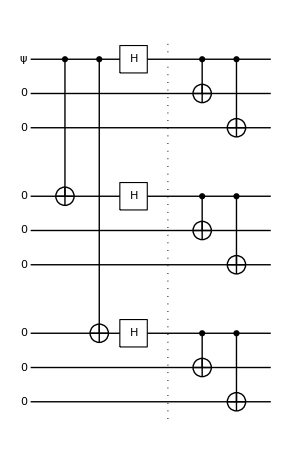
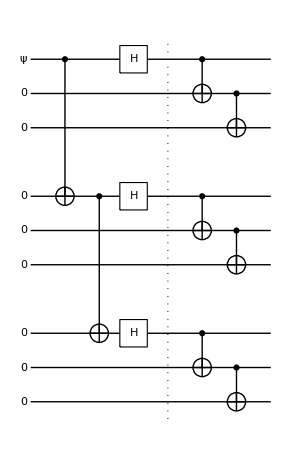
-Graphics-   and  -Graphics-,

or their equivalent variants. The first part of each quantum circuit, which is separated from the latter part by the vertical dotted line, is for the phase-flip encoding and the second part is to encode each block based on the bit-flip encoding.

The syndrome of the bit-flip error on the first block can be diagnosed by measuring the following two observables

(Z⊗Z⊗I)⊗(I⊗I⊗I)⊗(I⊗I⊗I) ,

(I⊗Z⊗Z)⊗(I⊗I⊗I)⊗(I⊗I⊗I) .

This is the way in which the bit-flip error is detected for a state encoded in three qubits. Similarly, the bit-flip errors on the rest of the blocks are diagnosed by measurement of the observables

(I⊗I⊗I)⊗(Z⊗Z⊗I)⊗(I⊗I⊗I) ,

(I⊗I⊗I)⊗(I⊗Z⊗Z)⊗(I⊗I⊗I) ,

(I⊗I⊗I)⊗(I⊗I⊗I)⊗(Z⊗Z⊗I) ,

(I⊗I⊗I)⊗(I⊗I⊗I)⊗(I⊗Z⊗Z) .

Once the qubit with the bit-flip error has been identified, the error can be corrected by applying X on the qubit.

The phase-slip error on any single qubit switches the relative sign in the encoded state of the whole block that it belongs to. Following the phase-flip correction code, it is thus sufficient to compare the signs of different blocks. The observable to compare signs of the first two blocks is

(X⊗X⊗X)⊗(X⊗X⊗X)⊗(I⊗I⊗I) .

Similarly, the signs of the second and third blocks can be compared through the measurement of the observable

(I⊗I⊗I)⊗(X⊗X⊗X)⊗(X⊗X⊗X) .

Once the block affected by a phase-flip error has been identified, applying the operator Z⊗Z⊗Z on the block recovers the original state.

So far, we have seen that the bit-flip and phase-flip errors on single qubits can be successfully detected and corrected as expected by constructing the code. Now the crucial point is that the same code can correct completely arbitrary errors as long as the error occurs in single qubits. Let ψ̄=000 c_0+111 c_1 be the initial state of the encoded qubits. Suppose that an error occurs in one of the qubits. The error can be efficiently described by a quantum operation ℱ. Suppose that ℱ is specified by the Kraus elements F_μ. Then, the state corrupted by the error is given by

ℱ(ψ̄ψ̄)=∑_μ F_μ ψ̄ψ̄ F_μ^† .

It is a statistical mixture of various pure states. Let us focus on one of them, say, F_μ ψ̄. As the Kraus element F_μ is an operator on a single qubit j, it can be expanded in the Pauli operators,

F_μ=I_j C_(0μ)+X_j C_(1μ)+Y_j C_(2μ)+Z_j C_(3μ) ,

where C_λμ are complex coefficients and the subscript j attached to the Pauli operators indicate that the operators act on the particular qubit j. Thus, the corrupted state F_μ ψ̄ is a superposition of the initial state ψ̄ without error, the state X_j ψ̄ affected by the bit-flip error, the state Z_j ψ̄ affected by the phase-flip error, and the state Y_j ψ̄=ⅈ X_j Z_j ψ̄ affected by both. When the error syndrome is diagnosed, the state collapses to the corresponding state, and the proper recovery operation discussed above brings back the initial state. The same procedure then applies to all other Kraus elements of ℱ.

This example clearly demonstrates that once the code can correct just bit-flip and phase-flip errors, then it can correct any arbitrary error. In other words, even though the errors in the qubits form a continuum, the fate of a quantum error-correction code is determined by its ability to correct a discrete set of errors. This is more rigorously established in the discretization theorem of quantum errors.

### Demonstration 1

Here is a widely known quantum circuit model for Shor’s 9-qubit quantum error correction code.

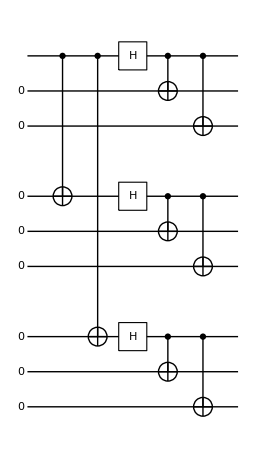

```mathematica
qc=QuantumCircuit[
LogicalForm[Ket[],S@Range[2,9]],
CNOT[S[1],S[4]],CNOT[S[1],S[7]],
S[{1,4,7},6],
{CNOT[S[1],S[2]],CNOT[S[4],S[5]],CNOT[S[7],S[8]]},
{CNOT[S[1],S[3]],CNOT[S[4],S[6]],CNOT[S[7],S[9]]},
"Invisible"->S@{3.5,6.5}
]
```

This is the logical basis state 0of the 9-qubit code.

```mathematica
out0=ExpressionFor@QuantumCircuit[Ket[S[1]->0],qc];
KetFactor@LogicalForm[out0,S@Range[9]]
```

((0_S_10_S_20_S_3+1_S_11_S_21_S_3)⊗(0_S_40_S_50_S_6+1_S_41_S_51_S_6)⊗(0_S_70_S_80_S_9+1_S_71_S_81_S_9))/(2 √2)

This is the logical basis state 1of the 9-qubit code.

```mathematica
out1=ExpressionFor@QuantumCircuit[Ket[S[1]->1],qc];
KetFactor@LogicalForm[out1,S@Range[9]]
```

((0_S_10_S_20_S_3-1_S_11_S_21_S_3)⊗(0_S_40_S_50_S_6-1_S_41_S_51_S_6)⊗(0_S_70_S_80_S_9-1_S_71_S_81_S_9))/(2 √2)

### Demonstration 2

Here is another equivalent implementation of Shor’s 9-qubit quantum error correction code.

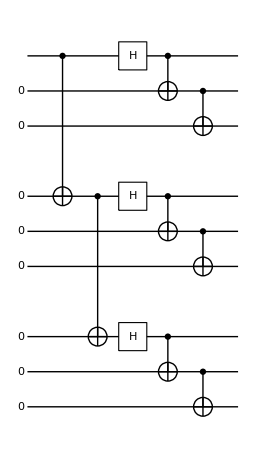

```mathematica
qc=QuantumCircuit[
LogicalForm[Ket[],S@Range[2,9]],
CNOT[S[1],S[4]],CNOT[S[4],S[7]],
S[{1,4,7},6],
{CNOT[S[1],S[2]],CNOT[S[4],S[5]],CNOT[S[7],S[8]]},
{CNOT[S[2],S[3]],CNOT[S[5],S[6]],CNOT[S[8],S[9]]},
"Invisible"->S@{3.5,6.5}
]
```

This is the logical basis state 0of the 9-qubit code.

```mathematica
out0=ExpressionFor@QuantumCircuit[Ket[S[1]->0],qc];
KetFactor@LogicalForm[out0,S@Range[9]]
```

((0_S_10_S_20_S_3+1_S_11_S_21_S_3)⊗(0_S_40_S_50_S_6+1_S_41_S_51_S_6)⊗(0_S_70_S_80_S_9+1_S_71_S_81_S_9))/(2 √2)

This is the logical basis state 1of the 9-qubit code.

```mathematica
out1=ExpressionFor@QuantumCircuit[Ket[S[1]->1],qc];
KetFactor@LogicalForm[out1,S@Range[9]]
```

((0_S_10_S_20_S_3-1_S_11_S_21_S_3)⊗(0_S_40_S_50_S_6-1_S_41_S_51_S_6)⊗(0_S_70_S_80_S_9-1_S_71_S_81_S_9))/(2 √2)

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Stabilizer Formalism
▪Stabilizer Codes
▪Quantum Error-Correction Codes
▪Quantum Information Systems with Q3

| Related Links
▪P. W. Shor, Physical Review A 52, R2493 (1995)https://doi.org/10.1103/PhysRevA.52.R2493, "Scheme for reducing decoherence in quantum computer memory."
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press, 2011).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer, 2022).